# 线性与非线性变换

## 2D空间

```mathematica
DynamicModule[{r,pts,pts2,vs,o},r=10;pts=Table[{x,y},{x,-r,r},{y,-r,r}];vs={{1,0},{0,1}};o={0,0};LocatorPane[Dynamic[vs],Dynamic[pts2=Map[vsᵀ.#&,pts,{2}];Graphics[{(*Line[pts],Line[ptsᵀ],*)Magenta,Line[pts2],Line[pts2ᵀ],Arrow[{o,vs[[1]]}],Arrow[{o,vs[[2]]}]},PlotRange->r,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],Axes->True]]]]
```

### 线性变换的特点

1. 原点不变
2. 等比例
3. 缩放，旋转，切变/投影

## 非线性变换

```mathematica
DynamicModule[{r,pts,pts2,fs,f,s=If[#>=0,1,-1]&},r=10;pts=Table[{x,y},{x,-r,r},{y,-r,r}];
fs={#&->"x",#^2&->"x^2",#^3&->"x^3",Exp->"e^x",
5Sin[#]&->"5sin(x)",5Cos[#]&->"5cos(x)",
{#[[1]],Norm[#]-#[[2]]}&->"x,norm(x)-y",
# Norm[#]^0.2&->"norm^0.2x",If[#=={0,0},#,2#/ Norm[#]^0.2]&->"x/norm^0.2",10Cos[#]Sin[#]&->"10cos(x)sin(x)",5{Cos[#[[1]]],Sin[#[[2]]]}&->"5cos(x),5sin(y)",
{Sin[#[[1]]]#[[2]]5,#[[1]]#[[2]]}&->"f4",
#-Cos[#]&->"x-cos(x)",
RotationMatrix[Norm[#]/5].#&->"rotate",
#+RandomReal[0.5,2]&->"random",Normalize[#]Abs[#[[1]]]&->"normalize(x)",Normalize[#]Max@Abs[#]&->"sphere",ReIm[(#[[1]]+I#[[2]])^2-1]/5&->"z^2-1",ReIm[(#[[1]]+I#[[2]])^3-1]/5&->"z^3-1",
#+0.5Sin[Norm[#]]&->"x+sin(nx)",
#+0.5Normalize[#] Sin[Norm[#]]&->"x+normalize(x)sin(x)",If[#[[1]]==#[[2]],#,(√2 s[#⟦2⟧] Norm[#] #)/(s[#⟦1⟧]s[#⟦2⟧]#[[1]]+#⟦2⟧)]&->"circle2square",
If[#[[1]]==#[[2]],#,Abs[(s[#⟦1⟧]s[#⟦2⟧]#[[1]]+#⟦2⟧)/(√2)]Normalize[#]]&->"square2circle",#+Sin[#]&->"x+sin",#+Reverse[Sin[#]]&->"x+rsin",
{{1,Cos[#[[2]]]},{Cos[#[[1]]],1}}.#&->"mcos.x"};
Column[{SetterBar[Dynamic[f],fs,Appearance->"Row"],
Dynamic[pts2=Map[f,pts,{2}];Graphics[{(*Line[pts],Line[ptsᵀ],*)Magenta,Line[pts2],Line[pts2ᵀ]},PlotRange->r,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],Axes->True,ImageSize->Large]]}]
]
```

#### Twitter

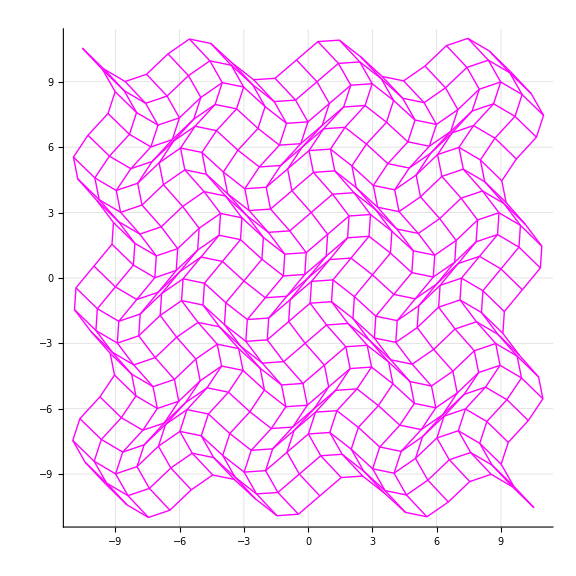

```mathematica
t="I need a job";r=10;a=Table[{x,y},{x,-r,r},{y,-r,r}];b=Map[#+Reverse[Sin[#]]&,a,{2}];Graphics[{Magenta,Line[b],Line[bᵀ]},PlotRange->r,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],Axes->True]
```

### 需要注意的点

```mathematica
{0,0}=={0,0}
{0,0}==0
```

True

{0,0}==0

```mathematica
Arg[{1,2}]
Arg[Complex@@{1,2}]
```

{0,0}

ArcTan[2]

```mathematica
Cos[{1,2}]
```

{Cos[1],Cos[2]}

```mathematica
Power[{1,2}]
```

{1,2}

```mathematica
Power[{1,2},2]
```

{1,4}

```mathematica
Power[2]
```

2

```mathematica
{Sin[#[[1]]]Cos[#[[1]]],Chop@Exp[(#[[2]])^3]}&[{10,-10}]
```

{Cos[10] Sin[10],1/ⅇ^1000}

### 这里遇到一个问题

```mathematica
Exp[-1000]
```

1/ⅇ^1000

```mathematica
Exp[-1000.]
```

General::munfl: Exp[-1000.] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

0.

```mathematica
Exp[IntegerPart[-1000.]]
Exp[IntegerPart[-1000.]]//N
N[Exp[IntegerPart[-1000.]],10]
```

1/ⅇ^1000

General::munfl: Exp[-1000.] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

0.

5.075958898×10^-435

```mathematica
N[Exp[-1000.],10]
```

General::munfl: Exp[-1000.] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

0.

## 3D

### 线性

```mathematica
DynamicModule[{r,s,pts,pts2,vs,o,x,y,z},r=10;s=4;pts=Table[{x,y,z},{x,-r,r,s},{y,-r,r,s},{z,-r,r,s}];o={0,0,0};{x,y,z}={1,1,1};

Column[{Slider[Dynamic[x],{-r,r}],Slider[Dynamic[y],{-r,r}],Slider[Dynamic[z],{-r,r}],
Dynamic[vs={{x,0,0},{0,y,0},{0,0,z}};pts2=Map[vs.#&,pts,{3}];Graphics3D[{{Dashed,Thin,Red,Map[Line,pts,{2}],Green,Map[Line,Transpose[pts,2<->3],{2}],Blue,Map[Line,Transpose[pts,1<->3],{2}]},{Thick,Red,Map[Line,pts2,{2}],Green,Map[Line,Transpose[pts2,2<->3],{2}],Blue,Map[Line,Transpose[pts2,1<->3],{2}]},Magenta,Arrow[{o,#}]&/@vs},
PlotRange->r,Axes->True,ImageSize->Large]]}]
]
```

这里用Slider或Silder2D都不够理想，可以使用Locator3D更好些，现在我懒得再修改了/(ㄒoㄒ)/~~

### 非线性

```mathematica
DynamicModule[{r,s,pts,pts2,fs,f},r=10;s=4;pts=Table[{x,y,z},{x,-r,r,s},{y,-r,r,s},{z,-r,r,s}];fs={#-Sin[#]&->"x-sin",Normalize[#]Abs[#[[1]]]&->"normalize(x)",Normalize[#]Max@Abs[#]&->"sphere",
#+0.5Normalize[#] Sin[Norm[#]]&->"x+normalize(x)sin(x)",# Norm[#]^0.2&->"norm^0.2x",Append[RotationMatrix[Norm[#]/5].#[[1;;2]],#[[3]]]&->"rotate2D",
RotationMatrix[Norm[#]/5,{1,1,1}].#&->"rotate3D"};

Column[{SetterBar[Dynamic[f],fs,Appearance->"Row"],
Dynamic[pts2=Map[f,pts,{3}];Graphics3D[{{Dashed,Thin,Red,Map[Line,pts,{2}],Green,Map[Line,Transpose[pts,2<->3],{2}],Blue,Map[Line,Transpose[pts,1<->3],{2}]},{Thick,Red,Map[Line,pts2,{2}],Green,Map[Line,Transpose[pts2,2<->3],{2}],Blue,Map[Line,Transpose[pts2,1<->3],{2}]},Magenta},
PlotRange->r,Axes->True,ImageSize->Large]]}]
]
```

#### Twitter

```mathematica
r=10;{m,l,t}={Map,Line,Transpose};a=Table[{x,y,z},{x,-r,r,4},{y,-r,r,4},{z,-r,r,4}];b=m[Normalize[#]Abs[#[[1]]]&,a,{3}];g={Red,m[l,#,{2}],Green,m[l,t[#,2<->3],{2}],Blue,m[l,t[#,1<->3],{2}]}&;Graphics3D[{{Dashed,Thin,g@a},{Thick,g@b}},Axes->True](*YUKI need a job*)
```

-Graphics3D-